Time elapsed: 28.696723

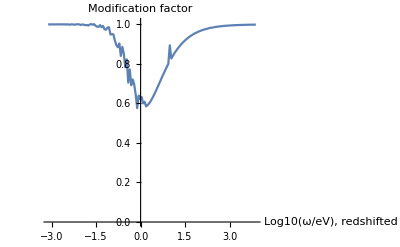

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

(*Массив значений энергий*)
omegaVal={};

(*Интервал энергий*)
lowerBound =-3;
upperBound =4;
step =0.05;

(*Параметры АЛП*)
g=6*10^(-20);
m=10^(-8);

(*Конфигурация поля НЗ*)
angle = Pi/3;
BSurf = 10^13;
R0 = 10;
period =3;

(*Размер области, должен быть равен радиусу*)
startingPoint = R0;

(*Радиус светового цилиндра*)
upperLimit=47713*period;

(*Значения поля (диполь)*)
(*Множитель плотности GJ*)
bRep={bRad->BSurf*Cos[angle]*(R0/(x+startingPoint))^3,
	bTheta->0.5*BSurf*Sin[angle]*(R0/(x+startingPoint))^3,
	bPhi->0,
	GJfactor->5};

(*Множитель плотности GJ*)


(*Элементы матрицы М*)
deltaMTheta:=5.0*10^7*bTheta*g;
deltaMPhi:=5.0*10^7*bPhi*g;

deltaMass:=2.5*10^9*m^2*(1/ω);

deltaPlasma:=GJfactor*3.1*10^(-12)*(bRad*Cos[angle]-bTheta*Sin[angle])*(1/period)*(1/ω);

deltaCEDTheta:=-4.5*10^(-22)*ω*bTheta^2;
deltaCEDPhi:=-4.5*10^(-22)*ω*bPhi^2;

(*Матрица М*)
mat:={{deltaPlasma+deltaCEDTheta,0,deltaMTheta},
	{0,deltaPlasma+deltaCEDPhi,deltaMPhi},
	{deltaMTheta,deltaMPhi,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
r[x_]:={{r11[x],r12[x],r13[x]},{r21[x],r22[x],r23[x]},{r31[x],r32[x],r33[x]}};

(*Список начальных условий*)r0={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};



t = Table[


(*Энергия на поверхности*)
ω0:=10^(k);

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/startingPoint))/(1-(4.134/(x+startingPoint)))];

(*Без красного смещения*)
(*ω:=ω0;*)

(*Решаем систему*)
eqs=NDSolve[Join[{ⅈ r'[x]==r[x].mat-mat.r[x]},r0],{r11[x],r22[x],r33[x]},{x,0,upperLimit}, MaxSteps->10^8, AccuracyGoal->5];
Re[r11[x]+r22[x]/.First[eqs]/.x->(upperLimit-1)]
,{k,lowerBound,upperBound,step}];

Print["Time elapsed: ",AbsoluteTime[]-time];

(*Строим ω с красным смещением*)
OmegaSurface:=10^x/.x->Range[lowerBound,upperBound,step];
zFactor:=Sqrt[(1-(4.134/startingPoint))];
OmegaInfinity:=OmegaSurface*zFactor;
OmegaInfinityLog:=Log10[OmegaInfinity];

(*Строим график*)
data=Transpose[{OmegaInfinityLog,t}];
plot = ListLinePlot[data,PlotRange->{{Min[OmegaInfinityLog],Max[OmegaInfinityLog]},{0.0,1.01}},AxesLabel->{"Log10(ω/eV),\nredshifted","Modification\nfactor"}, PlotMarkers->None]

(*Обычная шкала*)
(*dataToFile = Transpose[{10^x/.x->Range[lowerBound,upperBound,step],t}];*)

(*Логарифмическая шкала*)
dataToFile = Transpose[{OmegaInfinityLog,t}];

Export["Mixing.dat",dataToFile,"Table"];
```

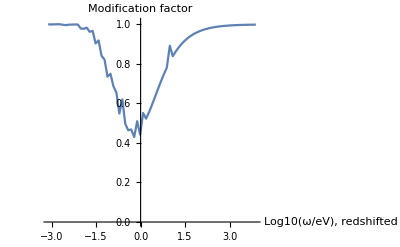

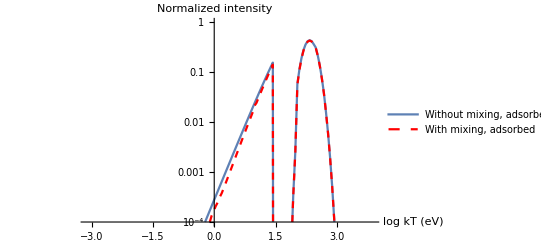

```mathematica
Clear["Global`*"]

(*Температура*)
T:=50;

(*Спектр ЧТ*)
Planck[w_]:=w^3/(4 Pi^3)/(Exp[w/T]-1);

(*Импорт данных*)
mixingResult = Import["Mixing.dat"];
energyLogValues=mixingResult[[All,1]];
energyValues = 10^x/.x->energyLogValues;
mixingValues = mixingResult[[All,2]];

(*Расчет спектра ЧТ и нормализация*)
planckValues := Planck[energyValues]/Max[ Planck[energyValues]];

(*Расчет спектра со смешиванием*)
mixedPlanckValues=planckValues *mixingValues;

(*Коэффициенты кривой поглощения*)
c0[x_]:=Piecewise[{
{17.3,0.030<x<=0.100},
	{34.6,0.100<=x<0.284},
	{78.1,0.284<=x<0.400},
{71.4,0.400<=x<0.532},
	{95.5,0.532<=x<0.707},
	{308.9,0.707<=x<0.867},
	{120.6,0.867<=x<1.303},
	{141.3,1.303<=x<1.840},
	{202.7,1.840<=x<2.471},
	{342.7,2.471<=x<3.210},
	{352.2,3.210<=x<4.038},
	{433.9,4.038<=x<7.111},
	{629.0,7.111<=x<8.331},
	{701.2,8.331<=x<10.000}},0];
c1[x_]:=Piecewise[{
{608.1,0.030<x<=0.100},
	{267.9,0.100<=x<0.284},
	{18.8,0.284<=x<0.400},
{66.8,0.400<=x<0.532},
	{145.8,0.532<=x<0.707},
	{-380.6,0.707<=x<0.867},
	{169.3,0.867<=x<1.303},
	{146.8,1.303<=x<1.840},
	{104.7,1.840<=x<2.471},
	{18.7,2.471<=x<3.210},
	{18.7,3.210<=x<4.038},
	{-2.4,4.038<=x<7.111},
	{30.9,7.111<=x<8.331},
	{25.2,8.331<=x<10.000}},0];
c2[x_]:=Piecewise[{
{-2150.,0.030<x<=0.100},
	{-476.1,0.100<=x<0.284},
	{4.3,0.284<=x<0.400},
{-51.4,0.400<=x<0.532},
	{-61.1,0.532<=x<0.707},
	{294.0,0.707<=x<0.867},
	{-47.7,0.867<=x<1.303},
	{-31.5,1.303<=x<1.840},
	{-17.0,1.840<=x<2.471},
	{0.0,2.471<=x<3.210},
	{0.0,3.210<=x<4.038},
	{0.75,4.038<=x<7.111},
	{0.0,7.111<=x<8.331},
	{0.0,8.331<=x<10.000}},0];

(*Сигма, кол-во атомов водорода *)
sigma[energy_]:=(c0 [energy]energy+c1[energy] energy+c2[energy] energy^2)energy^(-3)*10^(-24);
Nh:=12.9*10^(19);

(*Кривая поглощения, переводим энергию в keV*)
extinctionCurve[energyEv_]:=Exp[-sigma[energyEv*0.001]*Nh];

(*Modification factor для поглощения*)
adsorbtionValues:=extinctionCurve/@energyValues;

(*Расчет спектра с поглощением*)
adsorbedPlanckValues=planckValues*adsorbtionValues;

(*Расчет смешанного спектра с поглощением*)
adsorbedMixedPlanckValues = mixedPlanckValues*adsorbtionValues;

(*Нижняя граница графика*)
minVal:=10^(-4);

(*Вывод графиков, energyValues для обычной, energyLogValues для логарифмической*)
plotUnmixed = ListLogPlot[Transpose[{energyLogValues, planckValues}],
PlotRange->{{Min[energyLogValues],Max[energyLogValues]},{minVal,1}},PlotLegends->{"Without mixing" },Joined->True];

plotMixed =  ListLogPlot[Transpose[{energyLogValues, mixedPlanckValues}],PlotStyle->{Red,Dashed},
PlotRange->{{Min[energyLogValues],Max[energyLogValues]},{minVal,1}},PlotLegends->{"With mixing" },Joined->True];

plotUnmixedAdsorbed = ListLogPlot[Transpose[{energyLogValues, adsorbedPlanckValues}],
PlotRange->{{Min[energyLogValues],Max[energyLogValues]},{minVal,1}},PlotLegends->{"Without mixing, adsorbed" },Joined->True];

plotMixedAdsorbed = ListLogPlot[Transpose[{energyLogValues, adsorbedMixedPlanckValues}],PlotStyle->{Red,Dashed},
PlotRange->{{Min[energyLogValues],Max[energyLogValues]},{minVal,1}},PlotLegends->{"With mixing, adsorbed" },Joined->True];


Show[plotUnmixedAdsorbed ,plotMixedAdsorbed , AxesLabel->{"log kT (eV)","Normalized intensity"} ]
```

```mathematica
10^(1.9)
```

79.4328